```mathematica
(*parámetros iniciales*)
nLEDS = 250;
frames = 900;
r=1.3*1;h =6.5;
(*Cono*)
ℛ=Cone[{{0,0,0},{0,0,h}},r];
```

```mathematica
(*creación de puntos aleatorios - coordenadas cilídricas*)
(*altura aleatoria*)
rdmh=RandomReal[{0,h}];
(*ángulo*)
rdmangle= RandomReal[{0, 2Pi}];
(*radio circunferencia*)
rdmx=RandomReal[{0, (r(h-rdmh))/h}];
(*coordenadas de los puntos*)
posLEDS=Table[ (
rdmh=RandomReal[{0,h}];
rdmangle= RandomReal[{0, 2Pi}];
rdmx=RandomReal[{0.7 ((r(h-rdmh))/h), (r(h-rdmh))/h}];
{rdmx Cos[rdmangle],rdmx Sin[rdmangle],rdmh}),{i,1,nLEDS}];
Graphics3D[{AbsolutePointSize@5, Point@posLEDS, Opacity@0.5,ℛ }]
```

-Graphics3D-

```mathematica
posLEDS = {{-0.7133333333333334,-0.8400000000000001,0.3421052631578947},{-0.68,-0.46,0.68828320802005},{-0.7133333333333334,-0.12000000000000001,1.4091478696741855},{-0.013333333333333334,-0.52,2.244047619047619},{0.02,-0.4866666666666667,2.834586466165413},{-0.10666666666666667,-0.4266666666666667,3.596177944862155},{-0.4866666666666667,-0.3666666666666667,4.048245614035087},{-0.3866666666666667,-0.23333333333333334,4.830200501253133},{-0.32,-0.22666666666666668,5.469611528822055},{-0.19333333333333336,-0.23333333333333334,5.94204260651629},{-0.11333333333333334,0.36000000000000004,5.701754385964912},{-0.32,0.26666666666666666,6.031641604010025},{-0.2,-0.29333333333333333,5.404448621553884},{-0.2,-0.4066666666666667,4.948308270676692},{-0.22,-0.4066666666666667,4.239661654135338},{-0.03333333333333333,-0.45333333333333337,3.6246867167919796},{0.09333333333333334,-0.4866666666666667,3.095238095238095},{0.08,-0.56,2.402882205513784},{-0.02,-0.26666666666666666,1.6535087719298245},{-0.6666666666666667,-0.16,0.8593358395989974},{-0.7933333333333333,-0.6933333333333334,0.28916040100250623},{-0.8533333333333334,-0.07333333333333333,0.7656641604010025},{-0.49333333333333335,0.060000000000000005,1.6616541353383458},{-0.18666666666666668,0.19333333333333336,2.345864661654135},{-0.6066666666666667,0.28,3.0300751879699246},{-0.54,0.3866666666666667,3.702067669172932},{-0.4066666666666667,0.4,4.4718045112781954},{-0.31333333333333335,0.28,4.932017543859649},{-0.32,0.3466666666666667,5.510338345864661},{-0.2866666666666667,0.3066666666666667,6.088659147869674},{-0.2866666666666667,0.013333333333333334,6.31672932330827},{-0.14666666666666667,0.2866666666666667,6.007205513784461},{0.29333333333333333,0.35333333333333333,5.156015037593985},{-0.24666666666666667,0.39333333333333337,4.870927318295739},{-0.3066666666666667,0.44,4.284461152882205},{-0.6266666666666667,0.5533333333333333,3.921992481203007},{-0.6533333333333333,0.5933333333333334,3.282581453634085},{-0.8066666666666668,0.9600000000000001,2.6472431077694236},{-0.78,0.66,1.8489974937343356},{-0.7400000000000001,0.8400000000000001,1.119987468671679},{-0.06666666666666667,0.7733333333333334,1.1729323308270676},{-0.4066666666666667,0.8666666666666667,1.4417293233082706},{-0.36000000000000004,0.76,2.1055764411027567},{-0.3666666666666667,0.54,2.7531328320802},{-0.46,0.4733333333333334,3.0870927318295736},{-0.35333333333333333,0.49333333333333335,3.958646616541353},{0.16666666666666669,0.4466666666666667,4.492167919799498},{-0.44,0.4466666666666667,5.103070175438596},{-0.4,0.37333333333333335,5.595864661654135},{-0.29333333333333333,0.32,6.104949874686716},{-0.2733333333333334,0.3466666666666667,5.909461152882205},{-0.38,0.4266666666666667,5.237468671679197},{-0.32666666666666666,0.39333333333333337,4.94016290726817},{-0.5666666666666667,0.48000000000000004,4.080827067669173},{-0.6066666666666667,0.48000000000000004,3.5106516290726817},{-0.4666666666666667,0.7333333333333334,2.712406015037594},{-0.68,0.7466666666666667,2.43953634085213},{-0.22666666666666668,0.8866666666666667,1.2788220551378446},{-0.34,0.8866666666666667,1.0792606516290726},{0.42000000000000004,0.7666666666666667,0.24028822055137844},{0.62,0.64,0.806390977443609},{0.54,0.5266666666666667,1.7186716791979948},{0.5466666666666667,0.48000000000000004,2.162593984962406},{0.4733333333333334,0.49333333333333335,3.262218045112782},{0.5466666666666667,0.4866666666666667,3.3151629072681703},{0.4866666666666667,0.36000000000000004,4.215225563909774},{0.42000000000000004,0.32666666666666666,4.557330827067669},{0.39333333333333337,0.33333333333333337,5.13157894736842},{0.32666666666666666,0.36000000000000004,5.428884711779449},{0.4,0.24666666666666667,5.681390977443609},{0.,0.04,5.1763784461152875},{0.24000000000000002,-0.14,5.864661654135338},{0.22666666666666668,-0.16666666666666669,5.7669172932330826},{0.32,-0.1,4.866854636591478},{0.4666666666666667,-0.24000000000000002,4.699874686716791},{0.54,-0.14666666666666667,3.8853383458646613},{0.5,0.,3.5921052631578947},{0.30000000000000004,0.5266666666666667,2.6472431077694236},{0.29333333333333333,0.7133333333333334,2.406954887218045},{0.45333333333333337,0.5933333333333334,1.2869674185463658},{0.8733333333333334,0.6266666666666667,0.9611528822055138},{0.8933333333333334,0.5733333333333334,0.256578947368421},{0.3666666666666667,0.5733333333333334,0.3665413533834586},{0.66,0.5066666666666667,1.458020050125313},{0.49333333333333335,0.5,2.158521303258145},{0.4733333333333334,0.4,2.769423558897243},{0.52,0.4,3.3966165413533833},{0.2866666666666667,0.2866666666666667,4.097117794486215},{0.26666666666666666,-0.2733333333333334,4.422932330827067},{0.17333333333333334,-0.16666666666666669,5.461466165413533},{0.2866666666666667,0.3466666666666667,5.579573934837092},{0.3866666666666667,0.18000000000000002,6.166040100250626},{0.4466666666666667,0.5,5.648809523809524},{0.03333333333333333,-0.12000000000000001,5.9338972431077694},{0.02666666666666667,-0.13333333333333333,5.868734335839599},{0.13333333333333333,-0.2066666666666667,4.989035087719298},{0.28,-0.24666666666666667,4.781328320802005},{0.37333333333333335,-0.32666666666666666,3.759085213032581},{0.5666666666666667,-0.2733333333333334,3.653195488721804},{0.16,-0.36000000000000004,2.7409147869674184},{0.36000000000000004,0.31333333333333335,2.1544486215538847},{0.88,-0.17333333333333334,1.6209273182957393},{0.9,-0.37333333333333335,0.7412280701754386},{0.88,-1.04,0.6190476190476191},{0.3066666666666667,-0.62,1.0629699248120301},{0.36000000000000004,-0.52,1.6697994987468672},{0.17333333333333334,-0.5466666666666667,2.43953634085213},{0.013333333333333334,-0.49333333333333335,3.2296365914786964},{0.18000000000000002,-0.4866666666666667,3.5798872180451125},{0.4,-0.29333333333333333,4.390350877192982},{0.2866666666666667,-0.38,4.9605263157894735},{0.24666666666666667,-0.18666666666666668,5.388157894736842},{0.36000000000000004,-0.006666666666666667,6.0438596491228065},{0.3866666666666667,0.3866666666666667,5.147869674185463},{-0.19333333333333336,-0.2066666666666667,6.068295739348371},{-0.15333333333333335,-0.2,5.164160401002506},{-0.16666666666666669,-0.26666666666666666,5.046052631578947},{-0.2066666666666667,-0.34,4.117481203007519},{-0.07333333333333333,-0.19333333333333336,3.718358395989975},{0.31333333333333335,-0.36000000000000004,3.058583959899749},{0.14666666666666667,-0.64,2.8020050125313283},{0.3866666666666667,-0.5,1.6331453634085211},{0.46,-0.5333333333333333,1.119987468671679},{0.5133333333333334,-0.7466666666666667,0.24843358395989973},{-0.34,-0.4266666666666667,0.9855889724310777},{0.13333333333333333,-0.7933333333333333,1.800125313283208},{-0.07333333333333333,-0.52,2.4354636591478696},{-0.15333333333333335,-0.4,3.3233082706766917},{-0.04,-0.14666666666666667,3.702067669172932},{-0.17333333333333334,-0.3066666666666667,4.3129699248120295},{-0.1,-0.2066666666666667,4.9605263157894735},{-0.060000000000000005,-0.04666666666666667,5.6610275689223055},{-0.16,-0.23333333333333334,6.011278195488721},{0.,0.36000000000000004,4.773182957393484},{-0.18666666666666668,-0.24000000000000002,6.047932330827067},{-0.18666666666666668,-0.24666666666666667,5.681390977443609},{-0.21333333333333335,-0.1,4.801691729323308},{-0.4,0.09333333333333334,4.18671679197995},{-0.6266666666666667,0.44,3.7875939849624056},{-0.7000000000000001,0.4,2.87531328320802},{-0.5,-0.07333333333333333,1.9589598997493733},{-0.8600000000000001,0.14,1.3480576441102756},{-0.66,-0.22,0.44799498746867167},{-0.5933333333333334,-0.26,1.4702380952380951},{-0.49333333333333335,-0.30000000000000004,1.9060150375939848},{-0.4666666666666667,-0.24666666666666667,2.7409147869674184},{-0.35333333333333333,-0.31333333333333335,3.518796992481203},{-0.31333333333333335,-0.11333333333333334,4.422932330827067},{0.09333333333333334,0.15333333333333335,3.457706766917293},{-0.05333333333333334,-0.1,2.6228070175438596},{-0.6066666666666667,0.4666666666666667,0.9652255639097744},{-0.22,-0.3066666666666667,0.24436090225563908},{-0.7866666666666667,0.62,0.21585213032581452},{-0.26,-0.33333333333333337,0.268796992481203},{-0.6866666666666668,0.43333333333333335,1.2299498746867168},{-0.18666666666666668,-0.3466666666666667,1.9304511278195489},{-0.62,-0.11333333333333334,2.671679197994987},{-0.06666666666666667,-0.14666666666666667,2.7653508771929824},{0.17333333333333334,0.1,3.4210526315789473},{-0.35333333333333333,-0.3666666666666667,3.783521303258145},{-0.02666666666666667,0.26666666666666666,4.646929824561403},{-0.013333333333333334,0.013333333333333334,5.457393483709273},{0.17333333333333334,-0.26,4.357769423558897},{-0.006666666666666667,-0.21333333333333335,3.759085213032581},{0.2733333333333334,0.25333333333333335,3.225563909774436},{-0.16666666666666669,0.14666666666666667,2.195175438596491},{-0.28,0.2,1.8245614035087718},{0.14,-0.52,1.119987468671679},{0.7266666666666667,-0.4066666666666667,0.7656641604010025},{0.,0.16,0.17512531328320802},{-0.5133333333333334,0.6933333333333334,1.087406015037594},{0.32666666666666666,-0.22,1.1118421052631577},{-0.5,0.3666666666666667,1.963032581453634},{0.4466666666666667,0.006666666666666667,2.5046992481203008},{0.24666666666666667,-0.03333333333333333,3.4373433583959896},{0.22666666666666668,-0.24666666666666667,3.7061403508771926},{-0.12000000000000001,0.37333333333333335,4.4758771929824555},{0.17333333333333334,0.013333333333333334,5.526629072681704},{-0.08666666666666667,-0.060000000000000005,4.357769423558897},{0.013333333333333334,-0.09333333333333334,3.738721804511278},{0.18000000000000002,-0.28,3.0870927318295736},{-0.08666666666666667,0.08666666666666667,2.7042606516290726},{0.56,-0.09333333333333334,1.9915413533834585},{-0.26666666666666666,0.18666666666666668,1.8327067669172932},{0.45333333333333337,-0.02666666666666667,0.5213032581453634},{-0.12000000000000001,0.76,0.20363408521303256},{0.5266666666666667,0.6533333333333333,1.0426065162907268},{0.68,0.8533333333333334,2.1788847117794483},{-0.4066666666666667,0.3866666666666667,1.1729323308270676},{-0.45333333333333337,0.54,0.6271929824561403},{0.33333333333333337,0.9133333333333334,0.19548872180451127},{0.29333333333333333,0.8933333333333334,0.39097744360902253},{-0.4266666666666667,0.4066666666666667,1.2218045112781954},{0.6000000000000001,-0.060000000000000005,1.7390350877192982},{-0.31333333333333335,0.5066666666666667,2.382518796992481},{0.16666666666666669,-0.26666666666666666,3.3192355889724308},{0.013333333333333334,0.08666666666666667,3.4414160401002505},{-0.22666666666666668,0.11333333333333334,4.113408521303258},{-0.09333333333333334,0.42000000000000004,4.463659147869674},{-0.013333333333333334,0.013333333333333334,5.5062656641604},{0.006666666666666667,-0.14,3.5921052631578947},{-0.36000000000000004,0.24000000000000002,2.895676691729323},{0.14666666666666667,0.6666666666666667,2.362155388471178},{0.33333333333333337,-0.4133333333333334,1.7593984962406015},{-0.2866666666666667,0.26,1.763471177944862},{-0.19333333333333336,-0.09333333333333334,0.39097744360902253},{0.64,0.5066666666666667,0.3013784461152882},{1.4400000000000002,0.17333333333333334,0.5946115288220551},{0.8333333333333334,-0.4733333333333334,1.0588972431077694},{0.26,-0.5333333333333333,1.2177318295739348},{0.2,-0.7066666666666667,1.7471804511278195},{0.13333333333333333,-0.5666666666666667,2.9893483709273183},{-0.5933333333333334,-0.26,2.6431704260651627},{-0.6333333333333334,0.32,2.427318295739348},{-0.7733333333333334,0.7400000000000001,2.7409147869674184},{-0.18666666666666668,0.7666666666666667,2.2969924812030076},{0.25333333333333335,0.7400000000000001,2.6024436090225564},{0.68,0.4666666666666667,3.5921052631578947},{0.5933333333333334,-0.24000000000000002,3.75093984962406},{0.18666666666666668,-0.3066666666666667,4.088972431077694},{0.26666666666666666,-0.013333333333333334,4.984962406015037},{-0.14666666666666667,-0.32,5.119360902255639},{-0.4,-0.29333333333333333,5.489974937343358},{-0.37333333333333335,0.28,6.161967418546365},{0.3066666666666667,0.49333333333333335,5.563283208020049},{0.38,0.18000000000000002,5.7750626566416035},{0.26,-0.18000000000000002,5.384085213032582},{-0.2066666666666667,-0.5266666666666667,5.06234335839599},{0.02666666666666667,-0.2866666666666667,4.4147869674185465},{-0.5866666666666667,-0.4266666666666667,3.8975563909774436},{-0.6666666666666667,0.4266666666666667,3.8690476190476186},{-0.6000000000000001,0.5133333333333334,3.5839598997493733},{0.03333333333333333,0.6000000000000001,3.176691729323308},{-0.12666666666666668,0.7733333333333334,2.0648496240601504},{0.5133333333333334,0.7666666666666667,2.2073934837092732},{0.8533333333333334,0.5666666666666667,1.3154761904761905},{0.7533333333333334,-0.04666666666666667,0.9896616541353382},{0.4,-0.6666666666666667,1.6860902255639096},{0.5933333333333334,-0.5866666666666667,0.28916040100250623},{0.,-0.6266666666666667,1.6290726817042605},{-0.26,-0.6466666666666667,0.4357769423558897},{-0.78,-0.04666666666666667,0.2973057644110276},{-0.9400000000000001,0.31333333333333335,0.9204260651629073},{-0.7400000000000001,0.7866666666666667,0.7493734335839599},{-0.6333333333333334,0.8066666666666668,0.6271929824561403},{0.9266666666666667,0.9666666666666667,1.274749373433584},{1.2666666666666668,0.8733333333333334,1.3399122807017543},{0.7933333333333333,-0.2066666666666667,0.5457393483709273},{0.7733333333333334,-0.6666666666666667,0.41541353383458646},{-0.17333333333333334,-0.37333333333333335,0.30952380952380953}};
Graphics3D[{AbsolutePointSize@5, Point@posLEDS, Opacity@0.5,ℛ }]
```

-Graphics3D-

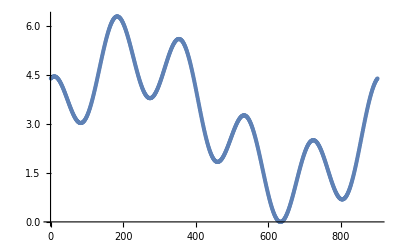

```mathematica
(*Curva por donde se va a mover la esfera*)
(*ángulo*)
fAngulo[f_]:=0.8Sin[(10π 0.2 f)/frames]+0.5Cos[(10π  f)/frames]
listatemp = fAngulo[f]/.f->Range[0,frames,1];
listaangulos = Rescale[listatemp,MinMax[listatemp],{0,2π}];
ListPlot[listaangulos]
```

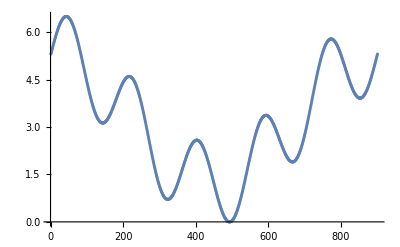

```mathematica
(*altura*)
fAltura[f_]:=0.5Sin[(10π  f)/frames]+0.8Cos[(10π 0.2 f)/frames]
listatemp = fAltura[f]/.f->Range[0,frames,1];
listaaltura = Rescale[listatemp,MinMax[listatemp],{0,h}];
ListPlot[listaaltura]
```

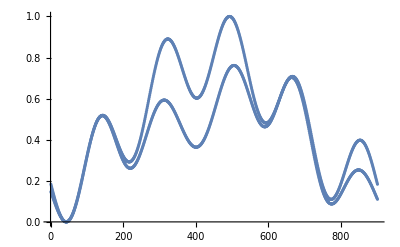

```mathematica
(*radio circunferencia*)
rtemp = (r(h-htemp))/h/.htemp->listaaltura;
ttemp=0.2Sin[(3.5π)/900 f]+0.8/.f->Range[0,frames,1];
listarho = rtemp*ttemp;
Show[
ListPlot[rtemp],
ListPlot[listarho]
]
```

```mathematica
(*curva de movimiento*)
curvaparam = Table[{listarho[[i]] Cos[listaangulos[[i]]],listarho[[i]] Sin[listaangulos[[i]]], listaaltura[[i]]},{i,1,frames}];
Show[Graphics3D[{Opacity@0.2,AbsolutePointSize@4, Point@posLEDS, Opacity@0.2,ℛ }],
ListPointPlot3D[curvaparam]]
```

-Graphics3D-

```mathematica
(*radio esfera que se mueve por la curva*)
raEsfera = 0.4;
```

```mathematica
(*Manipulación para revisar el movimiento*)
Manipulate[
(*solamente pintar los puntos que están en la esfera*)
valorVerdad = Map[RegionMember[Ball[curvaparam[[a]],0.5],#]&,posLEDS];
posVerdad := Flatten[Position[valorVerdad,True]];
puntosinsphere := posLEDS[[posVerdad]];
Show[
Graphics3D[{AbsolutePointSize@3, Point@puntosinsphere,Opacity@0.2,AbsolutePointSize@3, Point@posLEDS, Opacity@0.2,ℛ  }],
Graphics3D[{Opacity@0.2,Sphere[curvaparam[[a]],raEsfera]}],
ListPointPlot3D[curvaparam]],
{a,1,900,1}]
```

```mathematica
(*posición de los led que se prenden por fram (x900)*)
tablaposCurva = Table[
Flatten[Position[Map[RegionMember[Ball[curvaparam[[f]],raEsfera],#]&,posLEDS],True]],{f,1,900,1}
]
(*matriz 900 x 250 para saber cuales led se encienden*)
listatemp = ConstantArray[x,{900,250}];
For[i=1,i≤frames,i++,
(listatemp[[i]][[tablaposCurva[[i]]]]=y)]
(*vista*)
```

{{9,13,71,90,96,112,116,117,131,132,162,178,200,222,227},{9,13,71,90,112,116,117,132,136,162,178,200,222,227},{9,13,71,90,112,116,117,132,136,162,178,200,222,227},{9,13,71,90,112,116,132,136,162,178,200,222,227},{9,13,71,73,90,95,112,116,132,136,162,178,200,227},{9,13,71,73,90,95,112,116,132,136,162,178,200,227},{9,13,72,73,90,94,95,112,132,136,162,178,200,227},{9,10,13,72,73,90,94,95,112,132,136,162,178,200,227},{9,10,13,72,73,90,94,95,112,132,133,136,162,178,200},{9,10,13,72,73,90,94,95,132,133,136,162,178,200},{10,72,73,90,94,95,115,132,133,135,136,162,178,200},{10,72,73,90,94,95,115,132,133,135,136,162,178,200},{10,72,73,94,95,115,132,133,135,136,162,178,200},{10,72,73,94,95,115,132,133,135,136,200},{10,32,72,73,94,95,115,132,133,135,136},{10,32,72,73,94,95,113,115,132,133,135,136},{10,32,72,73,94,95,113,115,132,133,135,136},{10,32,72,73,94,95,113,115,132,133,135},{10,31,32,72,73,94,95,113,115,132,133,135},{10,31,32,72,94,95,113,115,133,135},{10,31,32,72,94,95,113,115,133,135},{10,31,32,72,94,95,113,115,133,135},{10,31,32,94,95,113,115,133,135},{10,31,94,95,115,133,135},{10,31,94,95,115,133,135},{31,94,115,133,135},{31,94,115,133,135},{31,94,115,133,135},{31,115},{31,115},{31},{31},{31},{31},{31},{31},{31},{31},{31},{31},{31},{31},{31},{31},{31},{31},{31},{31},{31},{31},{31},{31},{31},{31},{31},{31},{31,115},{31,115,135},{31,94,115,133,135},{31,94,115,133,135},{31,32,94,115,133,135},{10,31,32,94,95,115,133,135},{10,31,32,94,95,115,133,135},{10,30,31,32,94,95,115,133,135},{10,12,30,31,32,94,95,115,133,135},{10,12,30,31,32,72,94,95,115,133,135},{10,12,30,31,32,50,72,94,95,115,132,133,135},{10,12,30,31,32,72,94,95,115,132,133,135},{10,12,30,32,72,94,95,115,132,133,135,136},{10,12,30,32,51,72,73,94,95,115,132,133,135,136},{10,12,32,51,72,73,94,95,115,132,133,135,136,200},{10,11,12,32,51,72,73,94,95,115,132,133,135,136,200},{10,11,32,51,72,73,94,95,115,132,133,135,136,162,178,200},{10,11,32,72,73,94,95,115,132,133,135,136,162,178,200},{10,11,73,94,95,132,133,136,162,178,200},{9,10,11,94,95,132,136,162,178,200},{9,11,13,90,94,95,132,136,162,178,200},{9,11,13,29,90,95,132,136,162,178,200},{9,11,13,29,71,90,132,136,162,178,200},{9,13,29,71,90,116,132,136,162,178,200,223},{9,13,29,71,90,116,132,136,162,178,200,223},{9,13,29,71,90,116,132,136,162,178,200},{9,13,29,71,116,132,162,178,200},{9,13,71,116,117,162,200,222},{9,13,71,116,117,131,162,200,222},{13,28,71,116,117,131,137,162,200,222},{28,71,116,117,131,137,162,222},{8,28,71,116,117,131,137,222},{8,28,53,71,116,117,131,137,222},{8,28,34,53,71,116,117,131,137,222},{8,28,34,53,71,116,117,131,137},{8,28,34,53,116,117,131,137,161},{8,28,34,117,131,137,161},{8,28,131,137,148,161},{8,28,131,137,148,161,179},{8,28,137,148,161,179},{8,137,148,161,179},{8,130,137,138,148,179},{130,137,138,148,179},{130,137,138,148,179,198},{130,138,148,179,198},{15,118,130,138,148,179,198},{15,118,130,138,148,179,198},{7,15,118,130,138,148,179,198},{7,15,118,130,138,148,179,198},{7,15,118,130,138,148,179,198},{7,15,118,130,138,148,179,198},{7,15,118,130,138,148,160,198},{7,15,118,138,160,198,230},{7,118,119,138,160,198,230},{7,118,119,129,138,160,164,198,230},{7,118,119,129,147,160,164,230},{7,118,119,129,147,160,164,180,230},{6,7,118,119,129,147,160,164,180,230},{6,7,119,129,147,160,164,180,201,230},{6,7,16,119,129,147,160,164,180,201,230},{6,16,119,129,147,160,164,201,230},{6,16,119,128,129,147,160,164,201},{6,16,119,128,129,147,160,164,201},{6,16,119,128,129,147,160,164,201},{6,16,119,128,129,147,160,201},{6,16,119,128,129,147,160,201},{6,16,108,119,128,147,160,201},{6,16,108,128,147,160},{6,16,108,128,147},{6,16,108,128,147},{6,16,17,108,128,147},{6,16,17,108,128,147,196},{6,16,17,108,128,147,196},{6,16,17,108,128,147,196,212},{6,16,17,108,128,181,196,212},{6,16,17,108,128,181,196,212},{5,6,17,108,128,181,196,212},{5,17,108,128,181,196,212},{5,17,108,120,128,181,196,212},{5,17,108,120,128,181,196,212},{5,17,108,120,121,128,181,196,212},{5,17,108,120,121,128,181,196,212},{5,17,108,120,121,128,181,196,212},{5,17,108,120,121,128,181,196,212},{5,17,108,120,121,128,181,196,212},{5,17,108,120,121,128,181,196,212},{5,17,108,120,121,181,196,212},{5,17,108,120,121,181,196,212},{5,17,108,120,121,181,196,212},{5,17,108,120,181,196,212},{17,108,120,181,196,212},{17,108,120,181,196,212},{17,108,120,181,196,212},{17,108,120,181,196,212},{17,108,120,181,196,212},{17,108,120,181,196,212},{17,120,181,196,212},{17,120,175,181,196},{17,120,175,181,196},{120,175,181,196},{120,175,181,196},{120,175,181,196},{77,99,120,175,181,196},{77,99,120,175,181,196},{77,99,120,175,181,196},{77,99,120,159,175,181,196},{77,99,120,159,175,196},{77,99,159,175,176,196,219},{77,99,159,175,176,196,219},{77,98,99,159,175,176,196,219},{77,98,99,159,175,176,196,219},{77,98,99,159,175,176,196,219},{76,77,98,99,159,175,176,196,219},{76,77,98,99,159,175,176,219},{76,77,98,99,159,175,176,219},{76,77,98,99,159,175,176,219},{76,77,98,99,159,175,176,219},{76,77,98,99,159,175,176,219},{76,77,98,99,159,175,176,219},{76,77,98,99,175,176,219},{76,77,98,99,175,176,219},{76,77,98,99,175,176,219},{76,77,98,99,176,219},{76,77,88,98,99,176,219},{76,77,88,98,176,219},{76,77,88,98,176,219},{76,77,88,98,176,219,220},{76,88,98,176,219,220},{76,88,220},{76,88,220},{76,88,220},{76,88,220},{76,88,110,163,220},{76,88,89,110,163,220},{76,88,89,110,163,220},{88,89,110,163,220},{88,89,110,163,220},{88,89,110,163,220},{88,89,110,163,220},{88,89,110,163,220,229},{89,110,163,179,220,229},{89,110,163,179,220,229},{75,89,110,163,179,229},{75,89,110,163,179,229},{75,89,97,110,163,179,229},{75,89,97,110,163,179,229},{74,75,89,97,110,163,179,229},{74,75,89,97,110,163,179,229},{74,75,89,97,110,163,179,229},{74,75,89,97,110,163,179,229},{74,75,89,97,110,163,179,229},{74,75,89,97,110,163,179,229},{74,75,89,97,110,163,179,229},{74,75,89,97,110,163,179,229},{74,75,89,97,110,163,179,229},{74,75,89,97,110,163,179,229},{74,75,89,97,110,163,179,229},{74,75,89,97,110,163,179,229},{74,75,89,96,97,110,163,179,229},{74,75,89,96,97,110,163,179,229},{74,75,89,96,97,110,163,179,229},{74,75,89,96,97,110,163,179,229},{74,75,89,96,97,110,163,179,229},{74,75,89,96,97,110,163,179,229},{74,75,89,97,110,163,179,229},{74,75,89,97,110,163,179,229},{74,75,89,97,110,163,179,229},{74,75,89,97,110,130,163,179,229},{74,75,89,97,110,130,163,179,229},{75,89,97,110,130,163,179,229},{89,97,110,130,163,179,229},{89,97,110,130,163,179,229},{89,97,110,130,163,179,229},{15,89,97,110,130,163,179,220,229},{15,89,110,130,148,163,179,220,229},{15,89,110,130,148,163,179,220,229},{15,89,110,118,130,148,163,179,220,229},{15,89,110,118,130,148,163,179,220,229},{15,89,110,118,130,148,163,179,220,229},{15,89,118,130,148,163,179,220,229},{15,89,118,130,148,163,179,220,229},{15,89,118,130,148,163,179,220,229},{15,89,118,130,148,163,179,220,229},{15,89,118,130,148,163,179,220,229},{15,118,130,163,179,220,229},{15,118,130,163,164,179,220,229},{15,118,119,130,160,163,164,179,220,229},{7,15,118,119,129,130,160,164,180,220},{7,15,118,119,129,130,160,164,180,220},{6,7,15,16,118,119,129,130,160,164,180,220},{6,7,15,16,118,119,129,160,164,180,201,220},{6,7,16,118,119,129,147,160,164,180,201},{6,16,118,119,129,147,160,164,180,201},{6,16,118,119,129,147,160,164,180,201},{6,16,119,129,147,160,164,180,201},{6,16,119,128,129,147,160,164,180,201},{6,16,119,128,129,147,160,164,180,201},{6,16,119,128,129,147,160,164,180,201},{6,16,119,128,129,147,160,164,180,201},{6,16,119,128,129,147,160,164,201},{6,16,108,119,128,129,147,160,201},{6,16,108,128,147,201},{6,108,128,147},{108,128,147},{108,128,147},{108,128,147},{128,146},{128,146,158},{146,158},{146,158,213},{146,157,158,213},{146,150,157,158,213},{146,150,157,158,213},{146,150,157,158,213},{146,150,157,158,213},{146,150,157,158,213},{127,146,150,157,213},{127,146,157,213},{127,146,213},{213},{141,145,156},{141,145,156},{141,145,156},{141,145,156},{141,145,156},{141,145,156},{141,145,156},{141,145,156},{141,145,156},{141,144,145,156},{19,141,144,145,156},{19,144,145,156},{19,144,145,156},{19,144,145},{144},{144},{144},{125,144},{125,144},{125,144},{125},{125},{125},{125},{125},{125,168},{125,168},{125,168},{125,168},{125,168},{125,168},{125,168},{125,168},{125,168},{125,168},{125,168},{125,168},{168},{168},{168},{168},{168},{},{105},{105},{105},{105},{105},{105},{105},{105},{105},{105},{105,168},{105,168},{105,123,168},{105,123,168},{105,123,168,172},{105,123,168,172},{105,123,168,169,172},{105,123,168,169,172,210},{105,123,168,169,172,210},{105,123,168,169,172,210},{105,123,168,169,172,210},{105,123,168,169,172,210},{105,123,168,172,210},{105,123,168,172,210},{105,123,168,172,210},{105,123,168,172,210},{105,123,168,172,210},{105,123,168,172,210},{105,123,168,172,210},{105,123,168,172,210},{105,123,168,172,210},{105,123,168,172,210},{105,123,168,172,210},{105,122,123,168,172,210},{106,122,123,168,172,210},{106,122,123,172,210},{106,122,123,172,204,210},{106,122,172,204,210},{106,122,172,204,210},{106,122,204,210},{19,106,122,194,204,238},{19,106,122,194,204,238},{19,106,122,194,204,238},{19,106,122,194,204,238},{19,106,122,194,204,238},{19,106,122,194,204,238},{19,106,122,194,204,238},{19,106,122,183,204,238},{19,106,122,183,204,238},{19,106,122,183,204},{19,106,122,183,204},{106,122,183,204},{106,204},{4,204},{4,204},{4,204},{4,18,107,204},{4,18,107},{4,18,107,127},{4,18,107,127},{4,18,107,127},{4,18,107,127},{4,18,107,127},{4,18,107,127},{4,18,107,127},{4,18,100,107,127,150},{4,18,100,107,127,150},{4,18,100,107,127,150},{4,18,100,107,127,150},{4,18,100,107,127,150,158},{4,5,18,100,107,127,150,158},{4,5,18,100,107,127,150,158},{4,5,18,100,107,127,150,158},{4,5,18,100,107,127,150,158},{4,5,18,100,107,127,150,158},{4,5,18,100,107,127,150,158},{4,5,18,100,107,127,146,150,158},{4,5,18,100,127,146,150,158},{5,18,100,127,146,150,158},{5,100,127,146,150,158},{5,127,146,150,158,213},{127,146,150,158,213},{127,146,150,158,213},{127,146,150,157,158,213},{127,146,150,157,158,182,213},{127,146,150,157,158,182,213},{146,150,157,158,182,213},{146,150,157,158,182,213},{146,150,157,158,182,213},{146,150,157,158,182,213},{146,150,157,158,182,213},{146,150,157,158,182,213},{24,146,150,157,158,182,213},{24,146,150,157,158,182,213},{24,146,150,157,182,213},{24,146,150,157,182,213},{24,146,150,157,166,182,213},{24,146,150,157,166,213},{24,157,166,214},{24,157,166,214},{24,166,214},{24,166,214},{24,166,214},{24,166,214},{24,141,166,173,195,214},{24,141,166,173,195,214},{24,141,166,167,173,184,195,214},{24,141,166,167,173,184,195,214},{24,141,166,167,173,184,195,205},{24,141,166,167,173,184,195,205},{24,141,166,167,173,184,205},{24,141,166,167,173,184,205},{24,166,167,173,184,205},{166,167,173,184,205},{166,167,173,184,205},{166,167,173,184,205},{23,167,173,184,205},{23,167,173,184,205},{23,167,173,184,205},{167,173,184,205},{167,173,184,205},{167,184,205},{167,184,205},{167,184,193,205},{189,193,205},{189,193,205},{189,193},{41,189,193},{41,189,193},{41,58,189,193},{41,58,189,193},{41,58,189,193},{41,58,171,189,193},{41,171,189,193},{41,59,171,189,193},{41,59,171,189,193},{41,189,193},{41,189},{41,190},{190},{190},{190},{190},{190},{190},{190},{186,190},{186,190},{186,190},{186,190},{186,190},{186,190},{186,190},{186,190},{186,190},{186},{186},{186},{186},{186},{186},{186},{186},{186},{186},{153,186},{153},{153},{153},{153},{153},{153},{153},{153},{153},{153},{153},{153},{153},{153},{153},{153},{153},{153},{153,242},{153,242},{153,242},{242},{242},{242},{242},{242},{143,242},{143,242},{143,242},{143,242},{22,143,242},{22,143,242},{22,143,242},{20,22,143,242},{20,22,143,242},{20,22,143,242},{20,22,143,242},{20,22,143,242},{20,22,143},{20,22,143},{20,22},{20,22},{20,22},{20,22},{3,20,22},{3,20,22,142},{3,20,22,142},{3,20,142,144},{3,20,142,144},{3,142,144},{3,142,144},{3,23,142,144},{3,23,142,144},{3,23,142,144},{3,23,142,144},{3,23,142,144},{3,23,141,144},{3,23,141,144,145},{3,23,141,144,145},{23,141,145},{23,141,145,167},{23,141,145,167,173,184},{23,141,145,167,173},{23,141,145,173},{141,145,173},{141,173},{141,173,214},{141,173,214},{141,214},{24,214},{24,214},{24,157,214},{24,157,214},{24,157,195,214},{24,157,195,202,214},{24,44,140,157,195,202,214},{44,140,157,202,214},{25,44,140,202,214},{25,44,140,202,214},{25,44,45,140,202,214},{25,44,45,140,202},{25,44,45,140,202},{25,44,45,140,202},{25,44,45,140,202},{25,44,45,140,202},{25,44,45,140,202},{25,44,45,202},{25,44,45,202,233},{25,44,45,202,233},{25,44,45,202,233},{45,202,233},{45,202,233},{45,233},{45,233},{45,233},{45,233},{233},{149,165,233},{149,165,233},{149,165,233},{149,165,197,233},{149,159,165,197,233},{149,159,165,197,233},{64,149,159,165,197,233},{64,149,159,165,197,233},{64,87,149,159,165,197,233},{64,65,87,149,159,165,197,233},{64,65,87,149,159,165,197,233},{64,65,87,149,159,165,197,233},{64,65,87,149,159,165,197,233},{64,65,87,149,159,165,197,233},{64,65,87,149,159,165,197,233},{64,65,87,149,159,165,233},{64,65,87,149,159,165,233},{64,65,87,149,159,165},{64,65,87,149,159,165,175},{64,65,87,149,159,165,175},{64,65,87,149,159,165,175},{64,65,87,149,159,165,175},{64,65,87,149,159,165,175},{64,65,87,149,159,165,175},{64,65,87,149,159,165,175},{64,65,87,159,165,175},{64,65,87,159,165,175},{64,65,87,159,165},{64,65,87,159,165},{64,65,87,165},{64,65,87,165},{64,65,87,165},{64,165},{86,165},{86,165},{86,165},{86,165},{86},{86},{86},{86,174},{86,174},{86,174},{86,174},{86,174},{174},{174},{174},{174},{174},{174},{174},{174},{174},{174},{174},{174},{174,183},{174,183},{174,183},{174,183},{101,174,183},{101,174,183},{101,174,183},{101,183},{63,101,183},{63,101,183},{63,101,183},{63,85,101,183,194},{63,85,101,183,194},{63,85,101,183,194},{63,85,101,183,194},{63,85,101,183,194},{62,63,85,101,183,194},{62,63,85,101,183},{62,63,85,101,183},{62,63,85,101},{62,63,85,101},{62,63,85,101},{62,63,85,101},{62,63,85,101},{62,63,85,101},{62,63,85,101},{62,63,85,101},{62,63,85,101},{62,63,85,101},{62,63,85,101,235},{62,63,85,101,235},{62,63,85,101,235},{62,63,85,101,235},{62,63,85,101,235},{62,63,85,101,235},{62,63,85,101,235},{62,63,85,101,235},{63,85,101,203,235},{85,101,203,234,235},{85,203,234,235},{79,85,203,234},{79,203,234},{79,203,216,234},{79,203,216,234},{79,203,216,234},{43,79,203,216,234},{43,79,195,203,216,234},{43,79,195,203,216,234},{43,79,195,203,216,234},{43,195,203,216,234},{43,195,203,216,234},{43,195,203,216,234},{43,195,203,216,234},{24,44,195,203,216},{24,44,195,203,216},{24,44,56,195,216},{44,56,195,216},{44,56,195,216},{44,56,195,202},{44,56,195,202},{44,45,56,195,202},{44,45,56,202},{44,45,56,202},{25,44,45,56,140,202},{25,44,45,140,202},{25,44,45,140,202},{25,44,45,202},{25,44,45,202},{25,45,202},{25,45,202},{25,45,202},{25,45,55},{45,55},{26,55,232},{26,55,197,232},{26,55,197,232},{26,55,232},{26,46,55,139,232},{26,46,139},{26,46,139,198},{26,46,138,139,198},{26,46,138,198},{26,46,138,198},{35,46,138,198},{35,46,138,198},{35,46,138,179,198},{27,35,46,138,148,177,179,198},{27,35,138,148,177,179,198,199},{27,35,138,148,177,179,198,199},{27,35,138,148,161,177,179,198,199},{27,35,138,148,161,177,179,198,199},{27,35,138,148,161,177,179,198,199},{27,35,134,137,138,148,161,177,179,199},{27,28,34,134,137,148,161,177,179,199},{27,28,34,134,137,148,161,177,179,199},{27,28,34,53,134,137,148,161,177,199},{28,34,53,134,137,161,177,199},{28,34,53,134,137,161,177},{28,34,53,71,131,134,137,161},{28,34,53,71,131,134,137,161},{28,34,53,71,131,134,137,161},{28,34,53,71,116,131,134,137,161},{28,34,53,71,116,131,134,137},{28,34,53,71,116,131,134,137},{28,34,53,71,116,131,162},{28,53,71,116,162,200},{28,71,116,162,200},{71,116,162,200},{29,71,116,162,178,200},{29,71,116,132,162,178,200},{29,71,90,116,132,162,178,200},{11,29,71,90,132,162,178,200},{11,29,71,90,132,162,178,200},{11,29,71,90,132,162,178,200},{11,29,71,90,132,162,178,200},{11,29,71,90,132,162,178,200},{11,29,71,90,91,132,162,178,200},{11,29,90,91,95,132,162,178,200},{11,29,90,91,95,132,162,178,200},{11,29,73,90,91,94,95,132,136,162,178,200},{11,73,90,91,94,95,132,136,162,178,200},{11,73,90,91,94,95,132,136,162,178,200},{11,32,72,73,90,91,94,95,132,136,162,178,200},{11,32,72,73,94,95,132,136,162,178,200},{11,32,72,73,94,95,132,136,162,178,200,226},{11,32,72,73,94,95,132,136,162,178,200,226},{11,32,72,73,94,95,132,136,162,178,200,226},{11,32,72,73,94,95,132,136,162,178,200,226},{11,32,72,73,94,95,132,136,162,178,200,226},{11,32,72,73,94,95,132,162,178,200,226},{11,32,72,73,94,95,132,162,178,200,226},{11,32,72,73,94,95,132,162,178,200,226},{11,32,72,73,94,95,132,162,178,200,226},{11,32,72,73,94,95,132,162,178,200,226},{11,32,72,73,94,95,132,162,178,200,226},{11,32,72,73,94,95,132,162,178,200,226},{11,32,72,73,94,95,132,162,178,200,226},{11,32,72,73,94,95,132,162,178,200,226},{11,32,72,73,94,95,132,162,178,200,226},{11,32,72,73,94,95,132,162,178,200,226},{11,32,72,73,94,95,132,162,178,200,226},{11,32,70,72,73,90,91,94,95,132,162,178,200,226},{11,32,70,72,73,90,91,94,95,132,162,178,200,226},{11,70,72,73,90,91,94,95,132,162,178,200,226},{11,70,72,73,90,91,94,95,132,162,178,200,226},{11,70,72,73,90,91,94,95,132,162,178,200,226},{11,70,72,73,90,91,94,95,132,162,178,200,226},{11,70,72,73,90,91,94,95,132,162,178,200,226},{11,70,72,73,90,91,94,95,112,132,162,178,200,226},{11,70,72,73,90,91,94,95,112,132,162,178,200,226,227},{11,70,72,73,90,91,95,112,132,162,178,200,226,227},{11,69,70,71,73,90,91,95,112,132,162,178,200,226,227},{11,69,70,71,73,90,91,112,132,162,178,200,226,227},{11,69,70,71,73,90,91,112,132,162,178,200,227},{69,71,90,91,112,132,162,178,200,227},{69,71,90,91,112,132,162,178,200,227},{69,71,90,91,112,132,162,178,200,227},{69,71,90,91,112,132,162,178,200,227},{33,69,71,90,91,112,132,162,178,200,227},{33,69,71,90,112,132,162,178,200,221,227},{33,69,71,90,112,162,178,200,221,227},{33,69,71,90,112,162,178,200,221,227},{33,68,69,71,90,96,112,116,162,178,200,221,227},{33,68,71,90,96,112,116,162,178,200,221,227},{33,68,71,90,96,112,114,116,162,178,200,221,227},{33,68,71,74,96,114,162,221},{33,68,71,74,96,114,162,221},{33,68,71,74,96,114,131,221},{33,68,71,74,96,131,134,221},{33,68,71,74,96,131,134,221},{33,68,71,74,96,131,134,161,221},{33,71,74,96,131,134,161,221},{33,71,74,96,134,161,221},{71,74,96,134,161,221},{74,96,134,161,221},{74,134,161,221},{47,67,74,134,161,221},{47,67,74,134,161,221},{47,67,74,134,161,177,221},{47,67,74,134,161,177,199},{47,67,134,161,177,179,199},{47,67,134,161,177,179,199},{47,67,134,161,177,179,199},{47,67,134,161,177,179,199},{47,67,134,161,177,179,199},{47,67,88,161,177,179,199},{47,67,88,161,177,179,199},{47,67,88,161,177,179,199},{47,88,161,177,179,198,199},{47,88,161,177,179,198,199},{47,88,161,177,179,198,199},{47,88,177,179,198,199},{47,88,177,179,198,199},{47,88,177,179,198,199},{88,177,179,198,199},{88,177,179,198,199},{88,198},{88,198},{88,198},{88,198},{88,198},{88,198},{46,88,198},{46,88,198},{46,88,198},{46,88,198},{46,198},{46,180,198},{46,138,180,198},{46,138,180,198},{46,138,180,198},{46,138,180,198},{46,138,180,198},{46,138,180,198},{46,138,180,198},{46,138,180,198},{46,129,138,180,198},{46,129,138,180,198},{46,129,138,180,198},{129,138,180,198},{119,129,138,180,198},{119,129,138,180,198},{119,129,138,180,198},{119,129,138,180,198},{118,138,179,180,198},{118,138,179,180,198},{118,138,179,198},{118,138,148,179,198},{118,130,138,148,179,198},{118,130,138,148,179,198},{15,118,130,138,148,179,198},{15,118,130,138,148,179,198},{15,118,130,138,148,179,198},{15,118,130,138,148,179,198,229},{15,118,130,138,148,179,198,229},{15,118,130,138,148,179,198,229},{15,118,130,138,148,179,198,229},{15,118,130,138,148,163,179,198,229},{15,118,130,138,148,163,179,198,229},{15,118,130,138,148,163,179,198,229},{15,118,130,137,138,148,163,179,198,229},{15,130,137,148,163,179,229},{15,130,137,148,163,179,229},{130,137,148,163,179,229},{8,130,131,137,148,163,179,229},{8,130,131,137,148,179,229},{8,130,131,137,148,179,229},{8,14,96,117,131,137,148,179,229},{8,14,96,97,117,131,137,148,179,229},{8,14,96,97,116,117,131,137,222},{8,14,96,97,116,117,131,137,222},{8,14,71,74,96,97,116,117,131,137,221,222},{8,14,71,74,96,97,116,117,131,137,221,222},{8,14,71,74,96,116,117,131,137,221,222},{8,14,71,96,116,117,131,137,221,222},{14,71,96,116,117,131,137,221,222},{13,14,71,96,116,117,131,137,162,221,222},{13,14,71,96,112,116,117,131,137,162,221,222},{13,71,90,96,112,116,117,131,162,200,221,222,227},{9,13,71,90,96,112,116,117,131,162,178,200,221,222,227},{9,13,71,90,96,112,116,117,131,162,178,200,222,227}}

```mathematica
(*colores de los led-x y led-y*)
color1={0,255,255}; color2={255,0,0};
listatemp = listatemp/.{x->color1, y->color2};
(*Ejemplo del primer frame*)
listatemp[[1]]
(*se debe hacer flatten y lugo dividirlo nuevamente por Frames*)
listaFrames = Partition[Flatten[listatemp],nLEDS*3];
listaFrames[[1]]
```

{{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{255,0,0},{0,255,255},{0,255,255},{0,255,255},{255,0,0},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{255,0,0},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{255,0,0},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{255,0,0},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{255,0,0},{0,255,255},{0,255,255},{0,255,255},{255,0,0},{255,0,0},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{255,0,0},{255,0,0},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{255,0,0},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{255,0,0},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{255,0,0},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{255,0,0},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{255,0,0},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255}}

{0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,255,0,0,0,255,255,0,255,255,0,255,255,255,0,0,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,255,0,0,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,255,0,0,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,255,0,0,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,255,0,0,0,255,255,0,255,255,0,255,255,255,0,0,255,0,0,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,255,0,0,255,0,0,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,255,0,0,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,255,0,0,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,255,0,0,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,255,0,0,0,255,255,0,255,255,0,255,255,0,255,255,255,0,0,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255,0,255,255}

```mathematica
encabezado =Flatten[ Table[{StringJoin["R_",ToString[i]],StringJoin["G_",ToString[i]],StringJoin["B_",ToString[i]]},{i,0,nLEDS-1}]];
linea0 = Prepend[Range[frames],"FRAME_ID"];
PrependTo[listaFrames,encabezado];
listaFrames = Transpose[Prepend[Transpose[listaFrames],linea0]]
```

{1}
 |  |  |  |

```mathematica
Export["C:\\Users\\caramirezs\\My Drive\\Python\\WS2811\\curva.csv",listaFrames,"CSV", "TextDelimiters" -> ""]
```

C:\Users\caramirezs\My Drive\Python\WS2811\curva.csv